# Parallelized ACQE Three-qubit random Hamiltonian

## 1. Hamiltonian

```mathematica
AllPauli=Array[KroneckerProduct[KroneckerProduct[PauliMatrix[#1],PauliMatrix[#2]],PauliMatrix[#3]]&,{4,4,4}];
(*RR=RandomReal[{-10,10},{4,4,4}];*)
RR = {{{3.732288020871721,-6.5365143562568235,-4.34979111690048,-2.681145707053254},{8.528137446603978,-7.730191532118713,1.3360335238589869,-1.671347700710033},{-9.976443063114981,2.8233216130242482,-1.6074827376490042,-1.8080777136799924},{1.7565758135311391,-6.680159129735259,1.2655338326328511,-7.820390503136167}},{{-0.7871694653266204,-5.8879457699589395,-2.9485399429968666,-0.9041974413588783},{8.6754218188497,-2.326028497416644,9.421443083102695,0.280468132101376},{-2.727666650109825,-1.6861290260786213,4.780778335608048,2.837868052231606},{-2.881483899915839,3.3391208939337744,1.445863215184314,-7.412255336998264}},{{0.13327306373770753,-8.11954160631149,9.91177261357754,8.149117135879195},{4.576594842588797,1.5129734166115973,5.528169758503935,-7.962962359399249},{-5.241039734042964,-5.806925639754308,9.040384513564469,8.153221042203192},{-6.460372120689058,9.10296210961156,-9.91050009735186,-8.20130637528656}},{{-5.85278607591831,-3.951392622143466,-1.6381371179929936,9.997700587329994},{-8.15370522914052,6.013558336150695,0.9822481738608779,-8.192595909243614},{3.4203096053078497,-7.32392331111868,5.029145614945264,0.4128773638825436},{-1.455377117021829,1.9131589327441567,-9.24505785037795,0.168985631276243}}};(*The numbers of the calculation in the paper*)
Aux=AllPauli*RR;
Ham=ConstantArray[0,{8,8}];
For[i=1,i<=4,i++,For[j=1,j<=4,j++,For[k=1,k<=4,k++,Ham+=Aux[[i,j,k]]]]]
Ham = Re[Ham];
MatrixForm[Ham];
Eigenvalues[Ham]
```

{-66.7478,54.5665,-30.3615,28.788,-24.7941,22.5882,18.4945,-1.18196}

## 2. Antisymmetric operators

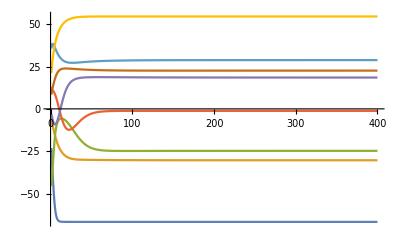

```mathematica
Ematrix=ConstantArray[0,{28,8,8}];
k=1;
For[n1=2,n1<=8,n1++,For[n2=1,n2<=n1-1,n2++,Ematrix[[k,n1,n2]]=1;Ematrix[[k]]=Ematrix[[k]]-Transpose[Ematrix[[k]]];k++]]
Commut[A_,B_]:=A .B - B. A;
Expect[ve1_,AA_]:=Conjugate[ve1].AA.ve1;
w=ConstantArray[0,{8}];
For[n3=1,n3<=8,n3++,w[[n3]]=n3];
w=w/Total[w];
Num=400;
Ene=ConstantArray[0,{Num,8}];
Vec=ConstantArray[0,{Num+1,8,8}];
Pro=ConstantArray[0,{Num,8}];
v=IdentityMatrix[8];
Vec[[1]]=v;
eta=-0.041;
For[m=1,m<=Num,m++,grad =ConstantArray[0,28];
For[i=1,i<=28,i++,For[j=1,j<=8,j++,grad[[i]] += w[[j]]*Expect[v[[j]],Commut[Ematrix[[i]],Ham]]]];
B=ConstantArray[0,{8,8}];
vv=ConstantArray[0,{8,8}];
For[i=1,i<=28,i++,B += grad[[i]]*Ematrix[[i]]];
For[j=1,j<=8,j++,vv[[j]] = MatrixExp[eta B].v[[j]];Vec[[m+1,j]]=vv[[j]];Ene[[m,j]]=Chop[Expect[vv[[j]],Ham]]];
v=vv]
ListPlot[{Ene[[All,1]],Ene[[All,2]],Ene[[All,3]],Ene[[All,4]],Ene[[All,5]],Ene[[All,6]],Ene[[All,7]],Ene[[All,8]]},Joined->True]
```

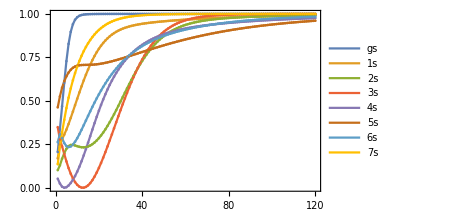

```mathematica
Num1=120;
BB=Ordering[Ene[[Num]]];
BB1=Ordering[Eigenvalues[Ham]];
Pro=ConstantArray[0,{Num1,8}];
For[m=1,m<=Num1,m++,For[j=1,j<=8,j++,Pro[[m,j]]=(Vec[[m,BB[[j]]]].Eigenvectors[Ham][[BB1[[j]]]])^2]]
ListPlot[{Pro[[All,1]],Pro[[All,2]],Pro[[All,3]],Pro[[All,4]],Pro[[All,5]],Pro[[All,6]],Pro[[All,7]],Pro[[All,8]]},Joined->True,AxesStyle->Directive[Black,8],TicksStyle->Directive[35],AxesStyle->Directive[Black,28],BaseStyle->{FontSize->14},Mesh->All, Frame->True,Mesh->40,PlotLegends->Placed[LineLegend[{Style["gs",FontSize->16],Style["1s",FontSize->16],Style["2s",FontSize->16],Style["3s",FontSize->16],Style["4s",FontSize->16],Style["5s",FontSize->16],Style["6s",FontSize->16],Style["7s",FontSize->16]},LegendFunction->Frame,Joined->Automatic,LegendLayout->{"Column",2}
],{0.75,0.4}]]
```

```mathematica
Export["out3.dat",Pro];
FilePrint["out3.dat"]
```

0.2054978276996779	0.168764930375922	0.10135672245362014	0.3486402426528373	0.052258148420898425	0.46244241504391126	0.26203351790074836	0.13541890293382086
0.3375887144627446	0.2470557031918939	0.12909904023160126	0.2775133431191636	0.02419028525006434	0.525514878322237	0.307589371784409	0.23737605290383038
0.4683160163010505	0.279162826132555	0.1670008673816442	0.238374713597959	0.006193099452034022	0.5754823524084656	0.28531185213188986	0.3178221271019875
0.6035944105058618	0.3055209573639983	0.19890920640121548	0.19480152229552275	0.00004554396222217071	0.6123157175324871	0.2570970107021429	0.39084982670509616
0.7282244919093258	0.3344941909724426	0.22403851641012126	0.1518050950674151	0.003266745566221758	0.6409487768507126	0.23983413418034977	0.45808638977988814
0.8275857654041944	0.36673292299750126	0.23958799332590844	0.11335356680049029	0.013001054670215818	0.6627599628579341	0.23400559346224797	0.5182327523193774
0.8970193066537346	0.4016068148144505	0.24615839349435806	0.0806234490138212	0.027467731576075245	0.6787619556860813	0.23755006348269125	0.5713747713786436
0.9408236439280664	0.4380593386624549	0.24640773236444258	0.05373304729975417	0.04579535471680342	0.6899789912981121	0.248390275779631	0.6182635486878479
0.9666176439410233	0.47512292474402734	0.243298444194236	0.0325031250282863	0.06763040332406363	0.6974232097092187	0.2647530183229139	0.6597819111596098
0.9812061917802718	0.5120738257539973	0.23914889916113805	0.01672757567947576	0.09281662276337485	0.7020392827063534	0.2851750908333253	0.6967201459219002
0.9893016286865105	0.5483816929923758	0.23546138087319066	0.006226614631108518	0.12119200043067122	0.7046601870745914	0.3084514190720328	0.7297172025208164
0.9937761754827984	0.5836315475819275	0.23310282887600478	0.0008418042925404109	0.15248376031815072	0.7059818754582238	0.3336004423044028	0.7592723948750294
0.9962669244745725	0.6174799904383236	0.23253012962008537	0.0004116555507158584	0.1862750064788047	0.7065557121574226	0.35983438796977457	0.7857776977420479
0.997675579043165	0.6496433438372246	0.233959431989998	0.0047460324117765155	0.2220205537104238	0.7067953341754903	0.3865352090751492	0.8095497482960679
0.9984911405226822	0.6799004878001467	0.2374722229206208	0.013607350072369498	0.2590916655731155	0.7069932159454815	0.41322980951814064	0.8308544897641722
0.9989777277981967	0.7080974113199658	0.24307663199399684	0.02670292834763614	0.2968327894842349	0.7073422537678917	0.43956608862129426	0.8499238973184433
0.9992785144838894	0.7341475430974748	0.2507409849059874	0.043688581720945	0.3346157146283446	0.7079583721006197	0.4652898657386345	0.866966303837918
0.9994718535159967	0.7580266853768083	0.26041125956079725	0.0641806215114869	0.3718820810575639	0.7089013879834991	0.4902242888191949	0.8821723033017478
0.9996012472234823	0.7797639341150142	0.27201933194212763	0.08777215418652995	0.40816970607972414	0.7101925711828013	0.5142521441103336	0.8957178771254528
0.9996913104512999	0.7994306277172051	0.285486068799273	0.1140497213125122	0.44312307791152483	0.7118283733630788	0.5373013948831631	0.9077659464926331
0.9997562964359589	0.8171291673659364	0.3007216341648081	0.14260741989729506	0.4764909300394513	0.7137904911541435	0.5593336835819522	0.9184671269371725
0.9998046838538327	0.8329829006433738	0.31762448436673507	0.17305704902885818	0.5081152261561857	0.7160528186878825	0.5803354381157396	0.927960152418029
0.9998416709693173	0.8471276579495641	0.33607999194500954	0.2050340605189242	0.5379156317157086	0.7185859782074895	0.6003110932980745	0.9363722212272043
0.999870550752576	0.8597050578219987	0.35595932039384903	0.23819993412207932	0.5658727836963429	0.7213600936481449	0.6192779883505215	0.9438193842818232
0.999893481564184	0.8708574386059188	0.37711894117548256	0.27224199587147824	0.5920125204100588	0.7243463639378198	0.6372625465828228	0.950407018405975
0.9999119273488104	0.8807241540524446	0.3994010134373645	0.30687176052027454	0.6163922727912957	0.7275178612395532	0.6542974259557551	0.956230386242771
0.9999269143852114	0.8894389564688556	0.42263470623228583	0.34182272073167397	0.6390900461546885	0.7308498557309631	0.6704193952191075	0.9613752650857769
0.9999391845150861	0.8971282193898413	0.44663843093900096	0.3768482544212206	0.660195952304779	0.7343198686072956	0.685667751830182	0.9659186203897747
0.9999492888669521	0.9039098001941615	0.4712228620793785	0.41172005303635484	0.6798059850505204	0.7379075810464534	0.7000831437473929	0.9699292998034111
0.9999576466996966	0.9098923881783388	0.4961945593113102	0.4462272404274124	0.6980176356003065	0.7415946760698322	0.7137066934893204	0.9734687268277478
0.9999645833698728	0.9151752222194321	0.5213599609466588	0.4801761723448277	0.714926936958113	0.7453646571597748	0.726579349206093	0.9765915775659352
0.9999703555264069	0.9198480903435958	0.546529500498762	0.5133907867692213	0.7306265734613916	0.7492026670700674	0.7387414071949693	0.9793464284329952
0.9999751683090685	0.9239915440945008	0.5715216010320094	0.5457133089750691	0.7452047556326579	0.7530953181981284	0.7502321645390544	0.9817763666195682
0.9999791874180801	0.9276772745294776	0.5961663253759456	0.5770050938886657	0.7587446274650789	0.7570305391087863	0.7610896710213938	0.9839195583563822
0.9999825478111127	0.9309686065926939	0.6203084995989826	0.6071474006695299	0.7713240321079534	0.7609974381883371	0.7713505571091517	0.9858097725850344
0.9999853601246899	0.9339210756702119	0.6438101775840153	0.6360419299774721	0.7830155104960722	0.7649861836310025	0.7810499204336191	0.9874768595655649
0.999987715520458	0.9365830557251807	0.6665523703258194	0.6636110029577488	0.7938864449446726	0.768987898191989	0.790221257354181	0.9889471853381412
0.9999896894132589	0.9389964130916943	0.6884360190000464	0.6897973140386029	0.8039992876975679	0.7729945669083772	0.7988964292932021	0.9902440239060086
0.9999913443862388	0.9411971643001849	0.7093822408881828	0.7145632402467897	0.8134118345031102	0.7769989560199055	0.807105655853551	0.9913879096150411
0.9999927325015677	0.9432161203288508	0.7293319181145522	0.7378897329720571	0.822177517371681	0.7809945414729071	0.8148775284860265	0.9923969525537222
0.999993897152814	0.9450795035136202	0.7482447286090008	0.7597748509749034	0.8303457002831299	0.7849754455854036	0.822239039812089	0.9932871199544235
0.9999948745635264	0.9468095269317459	0.766097736091349	0.7802320148050532	0.837961968037426	0.7889363806525166	0.8292156247344616	0.9940724865967719
0.999995695008593	0.9484249293473789	0.7828836618826477	0.7992880730733926	0.8450684026475499	0.7928725984605207	0.8358312102643737	0.9947654571392578
0.9999963838155816	0.9499414616845776	0.7986089577065376	0.8169812716892222	0.8517038443649296	0.7967798448476355	0.8421082716161873	0.9953769631683109
0.999996962189595	0.9513723234293139	0.8132917876620753	0.8333592103806866	0.8579041361151352	0.8006543185973449	0.848067892610637	0.9959166375790625
0.9999974478953267	0.9527285493275676	0.8269600117273889	0.8484768589287905	0.8637023511478689	0.8044926340758441	0.8537298288178627	0.99639296870663
0.9999978558227541	0.9540193482514954	0.8396492448489662	0.8623946908345524	0.8691290043102766	0.8082917871304803	0.8591125721840865	0.9968134364234634
0.9999981984574453	0.9552523971795445	0.8514010468791532	0.8751769765431942	0.8742122476880713	0.8120491238528637	0.8642334161383942	0.9971846322160358
0.9999984862723368	0.9564340939312772	0.862261280861007	0.8868902633626059	0.8789780515286595	0.8157623118809663	0.8691085203816061	0.9975123650586104
0.9999987280545845	0.9575697726737146	0.8722786614415162	0.8976020558532076	0.8834503714270857	0.8194293139713343	0.8737529747274143	0.9978017547168282
0.999998931178604	0.958663886338295	0.8815035020810865	0.9073796993145137	0.8876513027615682	0.8230483636177846	0.8781808615042864	0.9980573139414982
0.9999991018343818	0.9597201600180364	0.8899866594052087	0.916289460270509	0.8916012233354087	0.826617942528711	0.8824053161407794	0.9982830208543095
0.999999245218541	0.9607417192095264	0.8977786654231326	0.924395791513805	0.8953189251328527	0.830136759803199	0.886438585651286	0.9984823826825184
0.9999993656943453	0.961731196471641	0.9049290331472406	0.9317607650813582	0.8988217360375306	0.8336037326681605	0.8902920848173529	0.9986584918686625
0.9999994669257644	0.962690819731161	0.9114857180158661	0.9384436541772387	0.9021256322998706	0.8370179686559408	0.8939764499242401	0.9988140754634881
0.9999995519898521	0.9636224851043741	0.9174947160470843	0.9445006441672673	0.905245342477845	0.8403787491154623	0.897501589965619	0.9989515386047156
0.9999996234709879	0.9645278167449882	0.9229997794373411	0.949984652989286	0.9081944435158695	0.8436855139607603	0.9008767352729867	0.9990730027900518
0.9999996835399174	0.9654082158869624	0.9280422310111732	0.9549452423276027	0.9109854495708076	0.8469378475695114	0.9041104835619616	0.9991803395691272
0.9999997340200782	0.9662649009354414	0.9326608602244104	0.9594286024153383	0.9136298941423991	0.8501354657513066	0.9072108434164442	0.9992752002046981
0.9999997764432594	0.9670989401747271	0.9368918850789003	0.9634775951317176	0.9161384060182215	0.8532782037114529	0.9101852752545908	0.9993590417876895
0.9999998120963125	0.967911278411007	0.9407689661336035	0.9671318419820869	0.9185207795004422	0.8563660049412672	0.9130407298386817	0.9994331502325389
0.9999998420603724	0.9687027586489735	0.9443232606567061	0.9704278454624636	0.9207860393428676	0.8593989109703745	0.9157836844048752	0.9994986605279856
0.9999998672437802	0.9694741397137274	0.9475835067603048	0.9733991341326994	0.9229425007918686	0.8623770519206415	0.9184201764993324	0.9995565745732627
0.9999998884097328	0.9702261105698721	0.950576129031478	0.9760764233995072	0.924997825093259	0.8653006378051178	0.9209558356146667	0.9996077768898148
0.9999999061994982	0.9709593019554537	0.9533253586857545	0.9784877855135301	0.9269590707988352	0.8681699505188606	0.9233959127257704	0.999653048463634
0.9999999211519126	0.9716742958362354	0.95585336260518	0.9806588236022149	0.9288327411806048	0.8709853364717822	0.9257453078270614	0.9996930789424797
0.9999999337197574	0.9723716330927531	0.9581803767812413	0.9826128456937188	0.9306248280375259	0.8737471998167894	0.9280085955745364	0.99972847738516
0.9999999442835134	0.973051819775773	0.960324840669827	0.9843710356461168	0.9323408521584466	0.876455996229398	0.9301900491359937	0.9997597817362242
0.9999999531629137	0.9737153322027243	0.9623035297939359	0.9859526186952484	0.9339859006857185	0.8791122271978452	0.9322936623516305	0.9997874671785018
0.9999999606266537	0.9743626211160497	0.9641316846157663	0.9873750199907569	0.9355646616063091	0.8817164347853732	0.9343231703052217	0.9998119534975254
0.9999999669005402	0.9749941150823598	0.9658231342601372	0.9886540150210615	0.937081455581116	0.8842691968289138	0.9362820684033478	0.9998336115757221
0.9999999721743422	0.9756102232770717	0.9673904141228544	0.9898038712517838	0.9385402653082539	0.886771122540834	0.9381736300569481	0.9998527691200693
0.999999976607547	0.9762113377714433	0.9688448767567854	0.9908374806348252	0.939944762602331	0.8892228484826838	0.9400009230558235	0.9998697157144324
0.9999999803341953	0.9767978354164688	0.9701967957097348	0.991766482902023	0.9412983333589848	0.8916250348820779	0.941766824722845	0.9998847072768564
0.9999999834669436	0.9773700793999097	0.9714554622050183	0.992601379751209	0.9426041005620814	0.8939783622658991	0.943474035930558	0.9998979699924408
0.9999999861004765	0.9779284205380819	0.9726292747194002	0.9933516401752629	0.9438649454799736	0.8962835283849456	0.9451250940587052	0.9999097037839775
0.9999999883143769	0.9784731983521627	0.9737258216338013	0.9940257972862315	0.9450835271869322	0.8985412454069686	0.9467223849670213	0.9999200853750825
0.9999999901755359	0.9790047419692428	0.9747519572183414	0.9946315370552095	0.9462623005362755	0.9007522373567673	0.9482681540534662	0.9999292709940234
0.9999999917401761	0.9795233708806359	0.9757138712719838	0.9951757794314536	0.9474035327027829	0.9029172377836021	0.9497645164639666	0.9999373987606824
0.9999999930555554	0.9800293955837669	0.9766171527741684	0.9956647523269008	0.9485093184036045	0.9050369876376894	0.9512134665157367	0.9999445907940477
0.9999999941613971	0.9805231181289291	0.9774668479262565	0.9961040589596543	0.9495815938990803	0.9071122333389354	0.9526168863923429	0.9999509550731694
0.9999999950910916	0.981004832588184	0.9782675129682771	0.9964987390459241	0.9506221498675667	0.9091437250223725	0.9539765541649495	0.999956587080608
0.9999999958727068	0.9814748254604087	0.9790232621545885	0.99685332431744	0.9516326432415659	0.9111322149459727	0.9552941511905816	0.9999615712539546
0.9999999965298358	0.9819333760238581	0.9797378112632052	0.9971718888229598	0.952614608086074	0.9130784560476215	0.9565712689347964	0.9999659822679722
0.999999997082311	0.9823807566454968	0.9804145169996973	0.9974580944501152	0.953569465594117	0.9149832006390951	0.9578094152629236	0.9999698861672389
0.9999999975468055	0.9828172330546261	0.9810564126393894	0.9977152320789419	0.9544985332689121	0.9168471992258365	0.9590100202409106	0.9999733413668225
0.9999999979373335	0.9832430645869357	0.981666240232267	0.9979462587522292	0.955403033356897	0.9186711994422204	0.9601744414838992	0.9999763995364419
0.9999999982656766	0.9836585044039942	0.9822464796744964	0.9981538312211585	0.9562841005910764	0.9204559450928149	0.9613039690879098	0.99997910638176
0.9999999985417405	0.9840637996922683	0.9827993749295549	0.9983403361981846	0.9571427892996286	0.9222021752909174	0.9623998301774203	0.999981502334831
0.9999999987738502	0.9844591918450126	0.9833269576611068	0.9985079176233121	0.9579800799305439	0.9239106236863336	0.9634631930991788	0.9999836231643181
0.9999999989690072	0.984844916629786	0.9838310685194008	0.998658501225094	0.9587968850391996	0.9255820177750176	0.964495171290352	0.9999855005148487
0.9999999991330955	0.9852212043438304	0.9843133763033657	0.9987938166340345	0.9595940547821424	0.927217078283791	0.9654968268469482	0.9999871623837727
0.999999999271062	0.9855882799591827	0.9847753952018996	0.9989154172838571	0.9603723819570277	0.9288165186238914	0.9664691738165033	0.9999886335426236
0.999999999387067	0.9859463632590205	0.9852185003002494	0.9990246983152437	0.9611326066255388	0.9303810444076227	0.9674131812371486	0.999989935909715
0.9999999994846065	0.9862956689665168	0.9856439415208798	0.9991229126772759	0.9618754203532399	0.9319113530228283	0.9683297759434752	0.9999910888795724
0.9999999995666207	0.9866364068672256	0.9860528561528912	0.9992111856038827	0.962601470097644	0.9334081332603408	0.9692198451580107	0.9999921096142099
0.9999999996355811	0.986968781925866	0.9864462801098302	0.9992905276260462	0.9633113617733013	0.9348720649899473	0.9700842388856384	0.9999930133006942
0.9999999996935665	0.9872929943982057	0.9868251580426382	0.9993618462653446	0.9640056635204413	0.9363038188807831	0.9709237721269225	0.9999938133789101
0.9999999997423235	0.9876092399386422	0.9871903524224541	0.9994259565404934	0.9646849087015685	0.937704056162368	0.9717392269250228	0.9999945217429864
0.9999999997833207	0.9879177097039565	0.9875426516969685	0.9994835904058627	0.9653495986484754	0.9390734284228397	0.9725313542597208	0.9999951489194403
0.9999999998177937	0.9882185904536618	0.9878827776139657	0.9995354052293601	0.9660002051803142	0.940412577441182	0.9733008758009701	0.9999957042247369
0.9999999998467812	0.9885120646472806	0.9882113917965345	0.9995819914065616	0.9666371729117272	0.9417221350505325	0.9740484855333906	0.9999961959046568
0.9999999998711562	0.9887983105388214	0.9885291016460795	0.999623879198409	0.9672609213684658	0.9430027230298529	0.9747748512622134	0.9999966312575677
0.9999999998916531	0.9890775022687178	0.9888364656417291	0.999661544871145	0.9678718469265389	0.9442549530215094	0.9754806160102862	0.9999970167434747
0.999999999908888	0.9893498099534054	0.9891339980978657	0.9996954162093175	0.9684703245896134	0.9454794264724549	0.9761663993150065	0.9999973580804907
0.9999999999233811	0.9896153997727188	0.9894221734353137	0.9997258774655926	0.9690567096181818	0.9466767345969311	0.9768327984332954	0.9999976603301814
0.999999999935568	0.9898744340552394	0.9897014300161225	0.9997532738047205	0.9696313390229037	0.9478474583587512	0.9774803894620572	0.9999979279730709
0.9999999999458165	0.9901270713617278	0.9899721735868138	0.9997779152932214	0.9701945329335226	0.9489921684713805	0.9781097283809675	0.9999981649754496
0.9999999999544344	0.9903734665667253	0.9902347803704104	0.9998000804811447	0.9707465958537916	0.9501114254141884	0.9787213520238509	0.9999983748484801
0.9999999999616811	0.9906137709384255	0.9904895998434556	0.999820019617569	0.9712878178120088	0.9512057794633528	0.9793157789844009	0.9999985607005045
0.9999999999677751	0.9908481322168871	0.9907369572305135	0.9998379575372669	0.9718184754159381	0.9522757707360361	0.979893510461507	0.999998725283321
0.9999999999728995	0.991076694690644	0.9909771557453263	0.9998540962521746	0.9723388328201905	0.9533219292465551	0.9804550310490177	0.9999988710331404
0.9999999999772091	0.9912995992717794	0.9912104786048033	0.9998686172778567	0.9728491426134434	0.9543447749733611	0.9810008094743682	0.9999990001068274
0.9999999999808329	0.9915169835695083	0.9914371908393143	0.9998816837220988	0.9733496466322726	0.9553448179357538	0.9815312992901223	0.9999991144139726
0.99999999998388	0.9917289819623066	0.991657540920348	0.9998934421599734	0.9738405767078108	0.9563225582793295	0.9820469395221518	0.9999992156452794
0.9999999999864435	0.991935725668634	0.9918717622244201	0.9999040243172512	0.9743221553509057	0.9572784863692443	0.9825481552778472	0.9999993052976831
0.9999999999885982	0.9921373428162767	0.9920800743501577	0.99991354858178	0.9747945963809972	0.9582130828904415	0.9830353583174798	0.9999993846965859
0.999999999990411	0.9923339585103427	0.9922826843037389	0.9999221213604573	0.9752581055034767	0.9591268189540771	0.9835089475915824	0.9999994550155352
0.9999999999919347	0.9925256948999378	0.9924797875662966	0.9999298382976003	0.9757128808399028	0.9600201562094108	0.9839693097469421	0.9999995172936421
0.9999999999932172	0.9927126712435539	0.9926715690554742	0.9999367853689209	0.9761591134150707	0.9608935469605161	0.9844168196036234	0.9999995724509971